```mathematica
(*lu 163 *)
```

```mathematica
ClearAll["Global`*"]
```

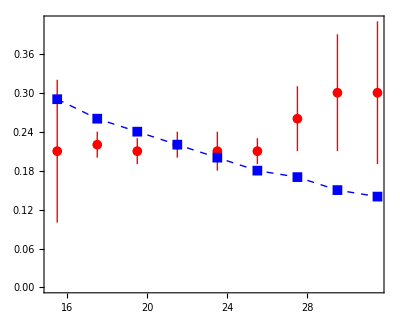

```mathematica
BE2outinTh={0.29,0.26,0.24,0.22,0.20,0.18,0.17,0.15,0.14};
BE2outinExp={0.21,0.22,0.21,0.22,0.21,0.21,0.26,0.30,0.30};
errorbarsBE2outin={0.11,0.02,0.02,0.02,0.03,0.02,0.05,0.09,0.11};
spins=Table[i/2,{i,31,63,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BE2outinExp[[i]],errorbarsBE2outin[[i]]]},{i,1,Length[BE2outinExp]}],Table[{spins[[i]],BE2outinTh[[i]]},{i,1,Length[BE2outinTh]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Arial"}]
```

```mathematica
(*lu 165 *)
ClearAll["Global`*"]
```

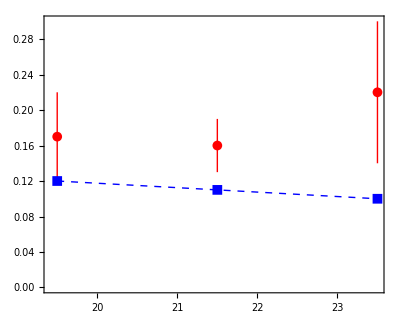

```mathematica
BE2outinTh={0.12,0.11,0.10};
BE2outinExp={0.17,0.16,0.22};
errorbarsBE2outin={0.05,0.03,0.08};
spins=Table[i/2,{i,39,47,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BE2outinExp[[i]],errorbarsBE2outin[[i]]]},{i,1,Length[BE2outinExp]}],Table[{spins[[i]],BE2outinTh[[i]]},{i,1,Length[BE2outinTh]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Arial"}]
```

```mathematica
(*lu 167 *)
ClearAll["Global`*"]
```

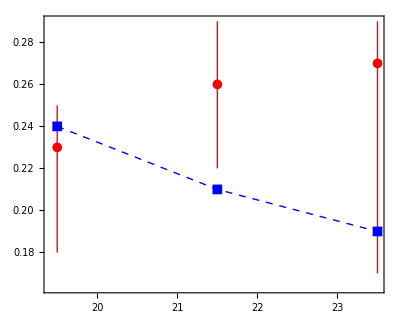

```mathematica
BE2outinTh={0.24,0.21,0.19};
BE2outinExp={0.23,0.26,0.27};
errorbarsBE2outinPlus={0.02,0.03,0.02};
errorbarsBE2outinMinus={0.05,0.04,0.10};
spins=Table[i/2,{i,39,47,4}];
p1=ListPlot[{Table[{spins[[i]],Around[BE2outinExp[[i]],{errorbarsBE2outinMinus[[i]],errorbarsBE2outinPlus[[i]]}]},{i,1,Length[BE2outinExp]}],Table[{spins[[i]],BE2outinTh[[i]]},{i,1,Length[BE2outinTh]}]},Joined->{False, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,FrameStyle->Directive[Black,Thick],PlotRange->All,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Arial"}]
```